Autor: Imię i nazwisko

# Metody numeryczne w technice

## (kierunek informatyka)

## Projekt 1

Metody Rungego-Kutty

Napisać procedury realizujące algorytmy metod Rungego-Kutty rzędu trzeciego i rzędu czwartego (argumenty:  f, x_0, y_0, h, n).

Korzystając z napisanych procedur wyznaczyć rozwiązanie przybliżone zagadnienia początkowego:

({y'(x)=(x y(x) - y^2(x))/x^2,
y(1)=2.)_□

Obliczenia wykonać dla 20 kroków o długości 0.1.

Na wspólnym rysunku wykreślić rozwiązanie dokładne oraz uzyskane rozwiązania przybliżone.
Wykreślić także, na jednym rysunku, błędy uzyskanych rozwiązań przybliżonych.

## Rozwiązanie

```mathematica
(*Metoda Rungiego - Kutty rzędu 3-go*)
(* Rozwiązanie dokładne *)
roz = DSolve[{y'[x] == (x*y[x]-(y[x])^2)/x^2,y[1] ==2}, y[x],x]
```

{{y[x]→(2 x)/(1+2 Log[x])}}

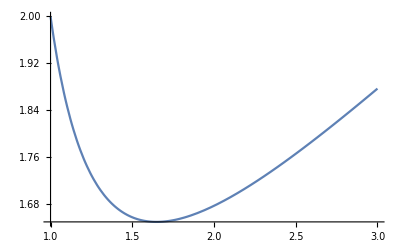

```mathematica
pdok = Plot[roz⟦1,1,2⟧,{x,1,3}, PlotRange -> All]
```

```mathematica
(*Metoda aproksymacji Rungiego - Kutty rzędu 3-go*)
Clear[metodaRK3];
metodaRK3[f_,x0_,y0_,h_,n_] :=Module[{xw,yw,k1,k2,k3,wynik},
xw = Table[x0+i*h,{i,0,n}];
yw = Table[0,{i,0,n}];
yw[[1]] = y0;
Do[
k1=f[xw[[i]],yw[[i]]];
k2 = f[xw[[i]]+h/2,yw[[i]]+h*k1/2];
k3 = f[xw[[i+1]],yw[[i]]-h*k1+2*h*k2];
yw[[i+1]] = yw[[i]] + h/6*(k1+4k2+k3),
{i,1,n}];
wynik = Transpose[{xw,yw}];
Return[wynik]
]
```

```mathematica
(* Obliczenia *)
```

```mathematica
f[x_,y_] := (x*y-y^2)/x^2;
x0 = 1;
y0 = 2;
h = 0.1;
n = 20;

(* Rozwiązanie przykładu metodą Rungiego - Kutty rzędu 3 *)
wynik3 = metodaRK3[f,x0,y0,h,n]
```

{{1.,2},{1.1,1.84781},{1.2,1.75876},{1.3,1.70529},{1.4,1.67376},{1.5,1.65667},{1.6,1.64954},{1.7,1.64954},{1.8,1.6548},{1.9,1.66402},{2.,1.6763},{2.1,1.69096},{2.2,1.70752},{2.3,1.7256},{2.4,1.74491},{2.5,1.76523},{2.6,1.78637},{2.7,1.80819},{2.8,1.83057},{2.9,1.85343},{3.,1.87668}}

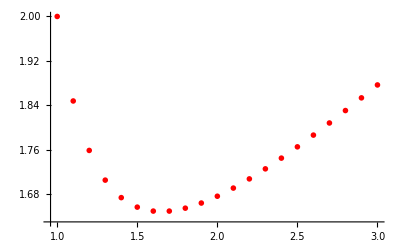

```mathematica
p3 = ListPlot[wynik3, PlotStyle-> {Red, PointSize -> 0.01}]
```

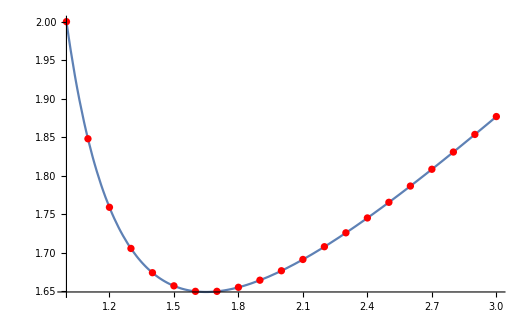

```mathematica
(* Wykres rozwiązania dokładnego i przybliżonego *)
Show[pdok,p3]
```

```mathematica
(* Wartości rozwiązania dokładnego w węzłach siatki *)
ydok = Table[roz[[1,1,2]] /. {x->wynik3[[i,1]]},{i,1,Length[wynik3]}]
```

{2.,1.84778,1.7587,1.70522,1.6737,1.65661,1.64948,1.64948,1.65474,1.66396,1.67624,1.69091,1.70747,1.72555,1.74486,1.76517,1.78631,1.80813,1.83052,1.85338,1.87663}

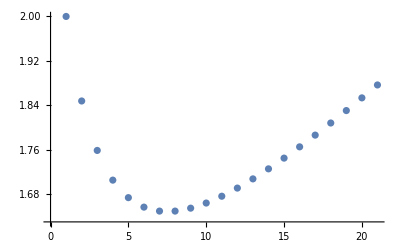

```mathematica
ListPlot[ydok]
```

```mathematica
(* Błędy w węzłach siatki *)
bledy3 = Table [{wynik3[[i,1]], Abs[wynik3[[i,2]] - ydok[[i]]]},{i,1,Length[wynik3]}]
```

{{1.,0.},{1.1,0.0000348491},{1.2,0.0000577547},{1.3,0.0000664135},{1.4,0.0000684173},{1.5,0.0000676717},{1.6,0.0000659031},{1.7,0.0000638544},{1.8,0.0000618383},{1.9,0.0000599772},{2.,0.0000583096},{2.1,0.0000568373},{2.2,0.0000555468},{2.3,0.0000544198},{2.4,0.0000534368},{2.5,0.00005258},{2.6,0.000051833},{2.7,0.0000511818},{2.8,0.0000506141},{2.9,0.0000501194},{3.,0.0000496887}}

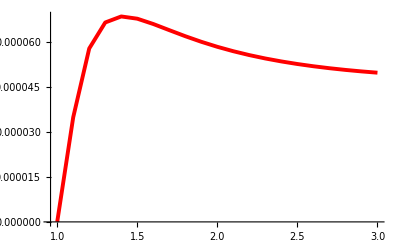

```mathematica
wb3 = ListPlot[bledy3, Joined->True, PlotStyle->{Red, Thickness -> 0.007}]
```